https://arxiv.org/pdf/1307.6925.pdf controlla

#### WW

```mathematica
subtract[x_]:=HeavisideTheta[x]HeavisideTheta[1-x]alpha/2/Pi(
-2(1-x)/x+2m2overq2max x +(1+(1-x)^2)/x Log[(1-x)/x^2/m2overq2max]
)
```

#### PDF delta

```mathematica
subtract[x_]:=(*HeavisideTheta[x]HeavisideTheta[1-x]*)alpha/2/Pi(
(1+(1-x)^2)/x Log[(1-x)/x^2/m2overq2max]
)
```

```mathematica
beta=alpha/Pi (Log[1/m2overq2max]-1)
```

(alpha (-1+Log[1/m2overq2max]))/π

```mathematica
PDFmu[x_]:=(*HeavisideTheta[x]HeavisideTheta[1-x]*)Exp[-EulerGamma beta+3/4 beta]/(Gamma[1+beta])beta(1-x)^(beta-1)
```

```mathematica
PDFmuOalpha[x_]:=Normal[Series[PDFmu[x],{alpha,0,1}]]
```

```mathematica
Simplify[PDFmuOalpha[t]]
```

-(alpha HeavisideTheta[1-t] HeavisideTheta[t] (-1+Log[1/m2overq2max]))/(π (-1+t))

```mathematica
PDFmuOalpha[x]/.{alpha->1/137,m2overq2max->(0.1/100)^2}/.t->0.2
```

0.153424

```mathematica
PDFmuOalpha[0.001]/.{alpha->1/137,m2overq2max->(0.1/100)^2}
```

0.304069

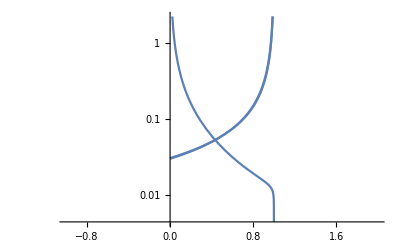

```mathematica
LogPlot[{subtract[x],PDFmu[x],PDFmuOalpha[x]}/.{alpha->1/137,m2overq2max->(0.1/100)^2},{x,-1,2}]
```

```mathematica
subtract[1/2]/.{alpha->1/137,m2overq2max->(0.1/1000)^2}
```

0.0531886

```mathematica
Convolve[DiracDelta[x],subtract[x],x,y]
```

(alpha (2-2 y+y^2) HeavisideTheta[1-y,y] Log[(1-y)/(m2overq2max y^2)])/(2 π y)

```mathematica
Convolve[PDFmuOalpha[x],subtract[x],x,y]
```

$Aborted

```mathematica
Integrate[DiracDelta[x-y]subtract[x],{x,0,1},Assumptions->1>=y>=0]
Integrate[DiracDelta[x]subtract[x-y],{x,0,1},Assumptions->1>=y>=0]
```

(alpha (2-2 y+y^2) HeavisideTheta[1-y,y] Log[(1-y)/(m2overq2max y^2)])/(2 π y)

-(alpha (2+2 y+y^2) HeavisideTheta[0] HeavisideTheta[-y,1+y] Log[(1+y)/(m2overq2max y^2)])/(2 π y)

```mathematica
convoluted[y_]:=NIntegrate[Simplify[ PDFmuOalpha[x]  subtract[x-y]]/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{x,0,1},AccuracyGoal->5]
```

```mathematica
NIntegrate[ PDFmu[x]  subtract[x-y]/.{alpha->1/137,m2overq2max->(0.1/1000)^2,y->0.91},{x,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910141}. NIntegrate obtained 0.768522 and 0.0603912 for the integral and error estimates.

0.768522

20.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0500582}. NIntegrate obtained 0.0489697 and 0.0119178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.101547}. NIntegrate obtained 0.0448005 and 0.0148107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.150375}. NIntegrate obtained 0.0351975 and 0.00548134 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{{0.05,0.0489697},{0.1,0.0448005},{0.15,0.0351975},{0.2,0.0368884},{0.25,0.0908626},{0.3,0.0550592},{0.35,0.0631156},{0.4,0.0510661},{0.45,0.0550155},{0.5,0.0869317},{0.55,0.0892152},{0.6,0.106677},{0.65,0.0922837},{0.7,0.245535},{0.75,0.181181},{0.8,0.443829},{0.85,0.631839},{0.9,0.883698},{0.95,NIntegrate[Simplify[PDFmuOalpha[x] subtract[x-0.95]]/.{alpha→1/137,m2overq2max→(0.1/1000)^2},{x,0,1},AccuracyGoal→5]},{1.,0.}}

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::inumri: The integrand -(0.0000470213 (4.8025-3.9 x+x^2) HeavisideTheta[1-x] HeavisideTheta[1.95-x] HeavisideTheta[-0.95+x] HeavisideTheta[x] Log[(1.×10^8 (1.95-1. x))/(-0.95+x)^2])/((-1.+x) (-0.95+x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.99999999999999999999999999997275243749960574466419003432897000423,0.99999999999999999994984934556026738265188276775117869296406617404}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

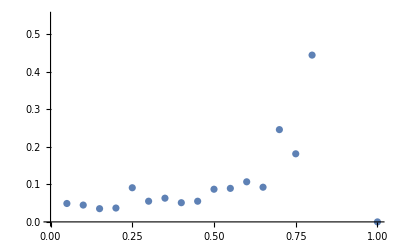

```mathematica
numeropunti=20.
input=Table[{i/numeropunti,convoluted[i/numeropunti]},{i,1,numeropunti}]
ListPlot[input]
```

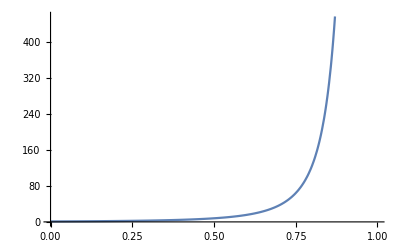

```mathematica
Plot[(1-x)^(-3),{x,0,1}]
```

```mathematica
subtract[1/2]/.{alpha->1/137,m2overq2max->(0.1/1000)^2}
```

0.055512

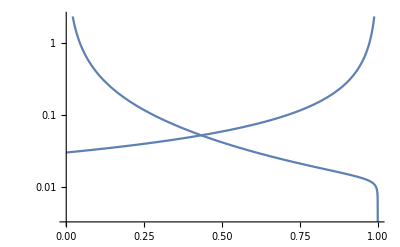

```mathematica
LogPlot[{subtract[x],PDFmu[x]}/.{alpha->1/137,m2overq2max->(0.1/100)^2},{x,0,1}]
```

```mathematica
PDFmu[0.2]/.{alpha->1/137,m2overq2max->(0.1/100)^2}
```

0.0377813

```mathematica
convoluted[0.2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.201156}. NIntegrate obtained 0.0365808 and 0.00613595 for the integral and error estimates.

0.0365808

```mathematica
LogPlot[convoluted[x],{x,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000332834}. NIntegrate obtained 0.0558279 and 0.00969945 for the integral and error estimates.

$Aborted

```mathematica
sumtractMellin=Integrate[Simplify[(subtract[x]x^(s-1))(*/.{alpha->1/137,m2overq2max->(0.1/100)^2}*)],{x,0,Infinity}]
```

ConditionalExpression[-(alpha (2+s-s^2 (10+s (7+2 s))+(-1+s) s (1+s) (2+s+s^2) Log[m2overq2max]+(-1+s) s (1+s) (2+s+s^2) (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2), Re[s]>1]

```mathematica
PDFmuMellin=Integrate[(PDFmu[x] x^(s-1)),{x,0,Infinity}]
```

ConditionalExpression[(alpha ⅇ^(-(alpha (-3+4 EulerGamma) (-1+Log[1/m2overq2max]))/(4 π)) Gamma[s] Gamma[-(alpha (1+Log[m2overq2max]))/π] (-1+Log[1/m2overq2max]))/(π Gamma[1+(alpha (-1+Log[1/m2overq2max]))/π] Gamma[-(alpha-π s+alpha Log[m2overq2max])/π]), Re[alpha (1+Log[m2overq2max])]<0&&Re[s]>0]

```mathematica
mellinconvresult=FullSimplify[sumtractMellin PDFmuMellin,Assumptions->{Re[alpha (1+Log[m2overq2max])]<0,Re[alpha]<Re[alpha Log[1/m2overq2max]], s>1}]
```

(alpha ⅇ^((alpha (-3+4 EulerGamma) (1+Log[m2overq2max]))/(4 π)) (Gamma[s] (-2+s (-1+s (10+s (7+2 s)))-(-1+s) s (1+s) (2+s+s^2) Log[m2overq2max])-(-2+s+s^3) Gamma[2+s] (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2 Gamma[-(alpha-π s+alpha Log[m2overq2max])/π])

```mathematica
mellinconv[t_]:=Evaluate[mellinconvresult]/.s->t
```

```mathematica
FullSimplify[mellinconv[s], Assumptions->s>1]
```

(alpha ⅇ^((alpha (-3+4 EulerGamma) (1+Log[m2overq2max]))/(4 π)) (Gamma[s] (-2+s (-1+s (10+s (7+2 s)))-(-1+s) s (1+s) (2+s+s^2) Log[m2overq2max])-(-2+s+s^3) Gamma[2+s] (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2 Gamma[-(alpha-π s+alpha Log[m2overq2max])/π])

```mathematica
Integrate[(x^(-(2+I z))mellinconv[2+I z])/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{z,-Infinity,Infinity}]
```

$Aborted

```mathematica
Integrate[(x^(-(c+I z))mellinconv[c+I z])/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{z,-Infinity,Infinity},Assumptions->c>0]
```

∫_(-∞)^∞ x^(-2-ⅈ z) mellinconv[2+ⅈ z]ⅆz

```mathematica
Integrate[(x^(-(c+I z)) (c+I z)^(-1)),{z,-Infinity,Infinity},Assumptions->{x>0,c>0}]
```

-π x^(c (-1-1/Sign[Log[x]])) (-1+Sign[Log[x]])

```mathematica
Integrate[x^(-(c+I z))mellinconv[c+I z]/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{z,-Infinity,Infinity},Assumptions->{x>0,c>0}]
```

$Aborted

```mathematica
f[x_]=x^2
g[x_]=x
```

x^2

x

```mathematica
Integrate[Normal[Simplify[Series[x^(-(c+I z))mellinconv[c+I z]/.{alpha->1/137,m2overq2max->(0.1/1000)^2,c->3,z->1/t},{t,0,1}]/.t->1/z]],{z,-Infinity,Infinity}]
```

SeriesData::sdatv: First argument 1/z is not a valid variable.

General::ivar: 1/z is not a valid variable.

SeriesData::sdatv: First argument 1/z is not a valid variable.

General::stop: Further output of SeriesData::sdatv will be suppressed during this calculation.

General::ivar: 1/z is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

SeriesData::sdatn: Order specification -1. in SeriesData[1/z,0,{6.283185307179586232,-15.9622797751599492244 ⅈ},-1.,2.,1.] is not a machine-sized integer.

SeriesData::sdatn: Order specification -1. in SeriesData[1/z,0,{-6.2831853071795864769,15.707963267948966192 ⅈ},-1.,2.,1.] is not a machine-sized integer.

Divide::infy: Infinite expression -1/0 encountered.

SeriesData::sdatn: Order specification -1. in SeriesData[1/z,0,{-1. ⅈ Log[x],-3.0000000000000004441 Log[x]+0.040475729232493762311 Log[1/z],0.102008465409685555869 ⅈ},-1.,2.,1.] is not a machine-sized integer.

General::stop: Further output of SeriesData::sdatn will be suppressed during this calculation.

Divide::infy: Infinite expression -1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

```mathematica
Integrate[subtract[x-y]PDFmuOalpha[x],x]
```

-1/(2 π^2 (1-y))alpha^2 (-1+Log[1/m2overq2max]) (x-x y-2 (-1+y) y Log[x-y]+(-1+y) (1+y) Log[1-x+y]-x (-1+y) Log[(1-x+y)/(m2overq2max (x-y)^2)]+(1+y^2) Log[-1+x] Log[(1-x+y)/(m2overq2max (x-y)^2)]-2 Log[x-y] Log[(1-x+y)/(m2overq2max (x-y)^2)]+(1+y^2) (Log[-1+x] (2 Log[(-x+y)/(-1+y)]-Log[(1-x+y)/y])+2 PolyLog[2,(-1+x)/(-1+y)]-PolyLog[2,(-1+x)/y])-2 (Log[x-y]^2+PolyLog[2,1-x+y]))

```mathematica
Integrate[subtract[x]PDFmuOalpha[x-y],x]
```

1/(2 π^2 (1+y))alpha^2 (-1+Log[1/m2overq2max]) (-x (1+y)+(1+y) Log[1-x]-x (1+y) Log[(1-x)/(m2overq2max x^2)]+2 Log[(1-x)/(m2overq2max x^2)] Log[x]-(1+y^2) Log[(1-x)/(m2overq2max x^2)] Log[-1+x-y]+2 (Log[x]^2+PolyLog[2,1-x])+(1+y^2) (Log[-1+x-y] (Log[(-1+x)/y]-2 Log[x/(1+y)])+PolyLog[2,(1-x+y)/y]-2 PolyLog[2,(1-x+y)/(1+y)]))

```mathematica
f[x_]=1/x^3
g[x_]=1/(1-x)^3
```

1/x^3

1/(1-x)^3

```mathematica
Limit[Integrate[f[x]g[x-y],{x,0+eps,1-eps},Assumptions->{0<eps<0.01,1>y>0}],eps->0]
```

DirectedInfinity[Sign[1+y]^2]/(1+y)^5

```mathematica
Limit[Integrate[f[x-y]g[x],{x,0+eps,1-eps},Assumptions->{0<eps<0.01,1>y>0}],eps->0]
```

ConditionalExpression[∞, y<0]

```mathematica
Integrate[f[x-y]g[x],x]
```

-((6 (-1+y))/(-1+x)+(6 (-1+y))/(x-y)+(-1+y)^2/(-1+x)^2-(-1+y)^2/(x-y)^2-12 Log[1-x]+12 Log[x-y])/(2 (-1+y)^5)